# Immediate vs deferred assignment

Katharine Long

Department of Mathematics and Statistics, Texas Tech University

There are a number of ways to assign values to variables. Full documentation is at: ["http://reference.wolfram.com/language/guide/Assignments.html"](http://reference.wolfram.com/language/guide/Assignments.html)
The most common assignment methods will be Immediate

### You will most often use immediate assignment (“=”)

Use this when the expression on the RHS of the assignment can be evaluated

```mathematica
f[x_]=Sin[x]/(1+x^2)
```

(sin(x))/(x^2+1)

The expressions 2 and (sin(x))/(1+x^2) can be evaluated at the time of assignment, so immediate assignment is used.

### Deferred evaluation (“:=”)

If the RHS of the assignment can’t be evaluated at the time of assignment, use deferred evaluation. This is easiest to explain by example .

#### Example: Writing a function to compute arc length of a function to be specified

Recall that the arc length of the curve defined by f(x) is

L=(∫_a)^b √(1+(df/dx)^2)dx.

We can’t evaluate the integral until the function f(x) has been specified. In writing a Mathematica function to evaluate arc length given a function f, we must use deferred evaluation.

```mathematica
arcLength[f_,a_,b_]:=Integrate[Sqrt[1+D[f,x]^2],{x,a,b}]
```

The arc length of a constant function f(x)=c on [0,1] is 1.

```mathematica
arcLength[c,0,1]
```

1

The arc length of f(x)=x on [0,1] is √2.

```mathematica
arcLength[x,0,1]
```

√2

The arc length of f(x)=1/2 x^2 is ∫_0^1 √(1+x^2)dx.

```mathematica
arcLength[x^2/2,0,1]
```

1/2 (√2+sinh^-1(1))

The arc length of sin(x) is an elliptic integral. There is no closed-form representation of this function.

```mathematica
arcLength[Sin[x],0,Pi/2]
```

√2 1/2

If the integral can’t be done in terms of known functions, it’s returned unevaluated.

```mathematica
arcLength[g[x],0,1]
```

∫_0^1 √((g'(x))^2+1)ⅆx

```mathematica
arcLength[Exp[-x^2+x],0,1]
```

∫_0^1 √(ⅇ^(2 x-2 x^2) (1-2 x)^2+1)ⅆx

#### Example: Writing a plotter for a function with a parameter

We can’t plot (x-t)^2 against x until the parameter t has been given a value.

```mathematica
doPlot[t_]:=Plot[(x-t)^2,{x,-2,2},PlotRange->{0,12}]
```

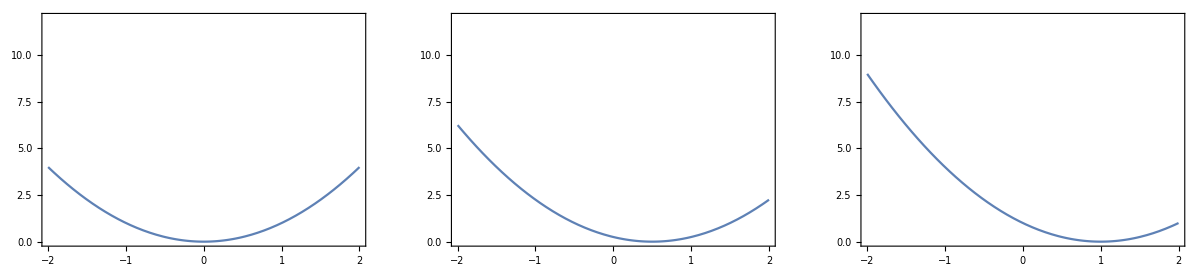

```mathematica
GraphicsRow[{doPlot[0],doPlot[1/2],doPlot[1]}]
```